```mathematica
mmax = 4;
n =.;
```

```mathematica
w[x_, y_] = Amn*Sin[m*Pi*x/a]*Sin[n*Pi*y/b];
Solve[Derivative[4,0][w][x,y]+2*Derivative[2,2][w][x,y]+Derivative[0,4][w][x,y]+px/D*Derivative[2,0][w][x,y]+py/D*Derivative[0,2][w][x,y]==0, px]//Simplify
```

{{px→((D m^4 π^2)/a^2+(a^2 D n^4 π^2)/b^4+(n^2 (2 D m^2 π^2-a^2 py))/b^2)/m^2}}

```mathematica
Solve[D/px*(Derivative[4,0][w][x,y]+2*Derivative[2,2][w][x,y]+Derivative[0,4][w][x,y])+Derivative[2,0][w][x,y]+ρ*Derivative[0,2][w][x,y]==0, px]//FullSimplify
```

{{px→(D (b^2 m^2+a^2 n^2)^2 π^2)/(a^2 b^4 m^2+a^4 b^2 n^2 ρ)}}

```mathematica
Clear[kad]
kad[ξ_,ρ_, m_, n_] = (((m/ξ)^2+n^2)^2)/((m/ξ)^2+n^2*ρ);
```

```mathematica
(* ξ=1, ρ=0, m=n=1 *)
Solve[D[kad[ξ, 0, 1, 1], ξ]==0, ξ]
kad[1, 0, 1, 1]
```

{{ξ→-1},{ξ→-ⅈ},{ξ→ⅈ},{ξ→1}}

4

```mathematica
(* ξ=1, ρ=1, m=n=1 *)
kad[1, 1, 1, 1]
```

2

```mathematica
(* ξ=1, ρ=-1 (trazione), m=1, n=1 *)
(*Solve[D[kad[ξ,-1, 1, 1], ξ]==0, ξ]*)
kad[1, -1, 1, 1]//N
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(* ξ=1, ρ=-1 (trazione), m=2, n=1 *)
(*Solve[D[kad[ξ,-1, 2, 1], ξ]==0, ξ]*)
kad[1, -1, 2, 1]//N
```

8.33333

```mathematica
(* ξ=1, ρ=-1 (trazione), m=2, n=1 *)
(*Solve[D[kad[ξ,-1, 2, 1], ξ]==0, ξ]*)
kad[1, -1, 1, 2]//N
```

-8.33333

```mathematica
ppy[ξ_, ρ_, m_, n_] = py/.Solve[(kad[ξ, ρ, m, n]/.ρ->py/px)==px, py][[1]]
```

(m^4+2 m^2 n^2 ξ^2-m^2 px ξ^2+n^4 ξ^4)/(n^2 ξ^4)

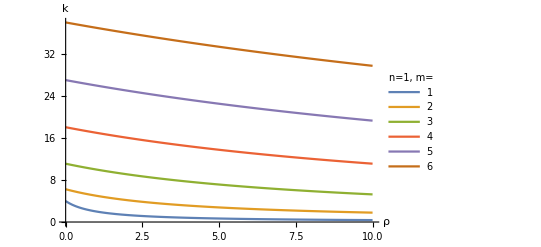

```mathematica
Plot[Evaluate@Table[kad[1, ρ, i, 1], {i, 1, mmax}], {ρ, 0, 10},AxesLabel->{"ρ", "k"}, PlotLegends->LineLegend[Range[mmax],  LegendLabel->"n=1, m="]]
```

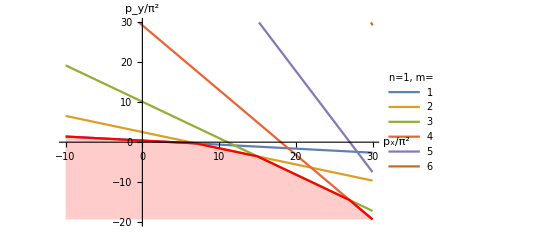

```mathematica
Show[
Plot[Evaluate@Table[ppy[1, ρ, i, 1]/Pi^2, {i, 1, mmax}], {px, -10, 30},AxesLabel->{"p_x/π^2", "p_y/π^2"}, PlotLegends->LineLegend[Range[6],  LegendLabel->"n=1, m="], PlotRange->{Automatic, {-20, 30}}],
Plot[Min[Evaluate@Table[ppy[1, ρ, i, 1]/Pi^2, {i, 1, mmax}]], {px, -10, 30}, PlotStyle->{Thick, Red}, Filling->Bottom]
]
```